```mathematica
logL[n_,m_,mus_,mub_,tau_] := (mus+mub) - n Log[mus+mub] +(tau*mub) - m Log[tau * mub]
```

```mathematica
bhathat:=Solve[D[logL[n,m,s,b,tau],b]==0, b] [[2]]
```

```mathematica
bhathat
```

{b→(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))}

```mathematica
mle :=Solve[D[logL[n,m,s,b,tau],{{s,b}}]==0,{s,b}]
```

```mathematica
mle
```

{{s→(-m+n tau)/tau,b→m/tau}}

```mathematica
loglambda
```

loglambda

```mathematica
logLMLE := logL[n,m,s,b,tau]/. mle[[1]]
```

```mathematica
logLMLE
```

m+m/tau+(-m+n tau)/tau-m Log[m]-n Log[m/tau+(-m+n tau)/tau]

```mathematica
logLCMLE := logL[n,m,s,b,tau] /.bhathat
```

```mathematica
logLCMLE
```

s+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))+(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))-m Log[(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))]-n Log[s+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))]

```mathematica
loglambda:=  logLCMLE - logLMLE
```

```mathematica
loglambda
```

-m+s-m/tau-(-m+n tau)/tau+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))+(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))+m Log[m]+n Log[m/tau+(-m+n tau)/tau]-m Log[(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))]-n Log[s+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))]

```mathematica
thislogLambda[ss_] :=loglambda /.  {n->100, m->50, tau->1, s->ss}
```

```mathematica
thislogLambda[s] /. s->50
```

0

```mathematica
thislogLambda[50]
```

0

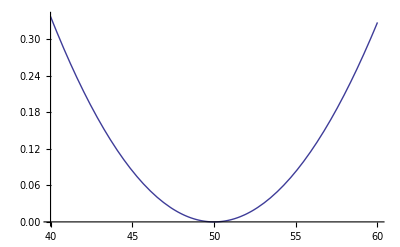

```mathematica
Plot[thislogLambda[x], {x,40,60}]
```

```mathematica
sigma = Simplify[D[loglambda, {s,2}]]
```

(8 m n (1+tau)^2 (m^2+2 m n+n^2+m s-n s+m s tau-n s tau+m √(4 m s (1+tau)+(m+n-s (1+tau))^2)+n √(4 m s (1+tau)+(m+n-s (1+tau))^2)))/(√(4 m s (1+tau)+(m+n-s (1+tau))^2) (m+n-s-s tau+√(4 m s (1+tau)+(m+n-s (1+tau))^2))^2 (m+n+s+s tau+√(4 m s (1+tau)+(m+n-s (1+tau))^2))^2)

```mathematica
Needs["CCodeGenerator`"]
```

```mathematica
c=Compile[{sigma},{n,m,s,tau}]
```

CompiledFunction[{sigma},{n,m,s,tau},-CompiledCode-]

```mathematica
c;
file = CCodeGenerate[{c},"sigmaExport"]
```

CCodeGenerate[{CompiledFunction[{sigma},{n,m,s,tau},-CompiledCode-]},sigmaExport]

```mathematica
c;
file = SymbolicCGenerate[{c},"sigmaExport"]
```

SymbolicCGenerate[{CompiledFunction[{sigma},{n,m,s,tau},-CompiledCode-]},sigmaExport]

```mathematica
file // ToCCodeString
```

ToCCodeString::unk: An unknown element, {TagBox[CompiledFunction[{8, 9.`, 5468}, {_Real}, {{3, 0, 0}, {3, 1, 0}}, « 3 », Function[{sigma}, {n, m, s, tau}], Evaluate], False, Rule[Editable, False]]}, , was found when generating code

CUnknownElement[SymbolicCGenerate[{CompiledFunction[{sigma}, {n, m, s, tau}, -CompiledCode-]}, sigmaExport]]

```mathematica
CForm[sigma]
```

(8*m*n*Power(1 + tau,2)*(Power(m,2) + 2*m*n + Power(n,2) + m*s - n*s + 
       m*s*tau - n*s*tau + m*Sqrt(4*m*s*(1 + tau) + 
          Power(m + n - s*(1 + tau),2)) + 
       n*Sqrt(4*m*s*(1 + tau) + Power(m + n - s*(1 + tau),2))))/
   (Sqrt(4*m*s*(1 + tau) + Power(m + n - s*(1 + tau),2))*
     Power(m + n - s - s*tau + Sqrt(4*m*s*(1 + tau) + 
         Power(m + n - s*(1 + tau),2)),2)*
     Power(m + n + s + s*tau + Sqrt(4*m*s*(1 + tau) + 
         Power(m + n - s*(1 + tau),2)),2))

```mathematica
sigma
```

2   2            2
(8 m n (1 + tau)  (m  + 2 m n + n  + m s - n s + m s tau - n s tau + 
 
                                                    2
      m Sqrt[4 m s (1 + tau) + (m + n - s (1 + tau)) ] + 
 
                                                    2
      n Sqrt[4 m s (1 + tau) + (m + n - s (1 + tau)) ])) / 
 
                                               2
  (Sqrt[4 m s (1 + tau) + (m + n - s (1 + tau)) ] 
 
                                                                     2  2
    (m + n - s - s tau + Sqrt[4 m s (1 + tau) + (m + n - s (1 + tau)) ])  
 
                                                                     2  2
    (m + n + s + s tau + Sqrt[4 m s (1 + tau) + (m + n - s (1 + tau)) ]) )

```mathematica
D[thislogLambda[x],{x,2}] /. x->50
```

1/150

```mathematica
sigma /. {n->100, m->50, tau->1, s->50}
```

1/150

```mathematica
F[qmu_,mu_,muprime_,sig_] := Evaluate[CDF[NormalDistribution[0,1],Sqrt[qmu]-(mu-muprime)/sig ]]
```

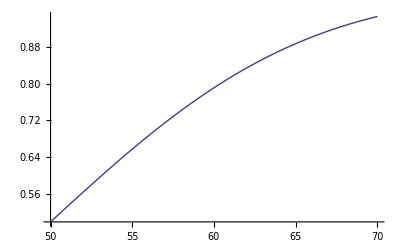

```mathematica
Plot[N[F[2*thislogLambda[x],x,x,sigma /. {n->100, m->50, tau->1, s->x}]] ,{x,50,70}]
```

```mathematica
Plot[N[F[2*loglambda,s,s,sigma] /. {n->100, m->50, tau->1, s->x}] ,{x,50,70}]
```

-Graphics-

```mathematica
sigma
```

(8 m n (1+tau)^2 (m^2+2 m n+n^2+m s-n s+m s tau-n s tau+m √(4 m s (1+tau)+(m+n-s (1+tau))^2)+n √(4 m s (1+tau)+(m+n-s (1+tau))^2)))/(√(4 m s (1+tau)+(m+n-s (1+tau))^2) (m+n-s-s tau+√(4 m s (1+tau)+(m+n-s (1+tau))^2))^2 (m+n+s+s tau+√(4 m s (1+tau)+(m+n-s (1+tau))^2))^2)

```mathematica
F[2*loglambda,s,s,sigma ]
```

1/2 Erfc[-√(-m+s-m/tau-(-m+n tau)/tau+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))+(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))+m Log[m]+n Log[m/tau+(-m+n tau)/tau]-m Log[(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))]-n Log[s+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))])]

```mathematica
sigma0 = sigma /. s->0
```

(8 m n (m^2+2 m n+n^2+m √((m+n)^2)+n √((m+n)^2)) (1+tau)^2)/(√((m+n)^2) (m+n+√((m+n)^2))^4)

```mathematica
F[2*loglambda,s,0,sigma0 ]
```

1/2 Erfc[1/(√2)((√((m+n)^2) (m+n+√((m+n)^2))^4 s)/(8 m n (m^2+2 m n+n^2+m √((m+n)^2)+n √((m+n)^2)) (1+tau)^2)-√2 √(-m+s-m/tau-(-m+n tau)/tau+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))+(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))+m Log[m]+n Log[m/tau+(-m+n tau)/tau]-m Log[(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))]-n Log[s+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))]))]

```mathematica
N[F[2*loglambda,s,s,sigma ]/(1-F[2*loglambda,s,0,sigma0 ]) /. {n->100, m->50, tau->1, s->50}]
```

0.5

```mathematica
Plot[N[F[2*loglambda,s,s,sigma ]/(1-F[2*loglambda,s,0,sigma0 ]) /. {n->100, m->50, tau->1, s->x}],{x,50,70}]
```

-Graphics-

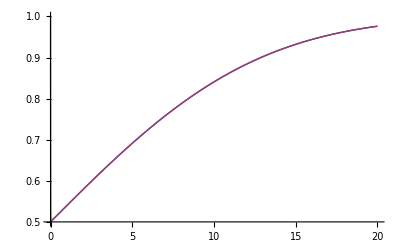

```mathematica
Plot[{N[F[2*loglambda,s,s,sigma] /. {n->50, m->50, tau->1, s->x}],N[F[2*loglambda,s,s,sigma ]/(1-F[2*loglambda,s,0,sigma0 ]) /. {n->50, m->50, tau->1, s->x}]}
,{x,0,20}]
```

```mathematica
Solve[F[2*loglambda,s,s,sigma ]==CLSB,s]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[1/2 Erfc[-√(-m+s-m/tau-(-m+n tau)/tau+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))+(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))+m Log[m]+n Log[m/tau+(-m+n tau)/tau]-m Log[(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))]-n Log[s+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))])]==CLSB,s]

```mathematica
Solve[F[2*loglambda,s,s,sigma ]/(1-F[2*loglambda,s,0,sigma0 ])==CLS,s]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Erfc[-√(-m+s-m/tau-(-m+n tau)/tau+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))+(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))+m Log[m]+n Log[m/tau+(-m+n tau)/tau]-m Log[(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))]-n Log[s+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))])]/(2 (1-1/2 Erfc[1/(√2)((√((m+n)^2) (m+n+√((m+n)^2))^4 s)/(8 m n (m^2+2 m n+n^2+m √((m+n)^2)+n √((m+n)^2)) (1+tau)^2)-√2 √(-m+s-m/tau-(-m+n tau)/tau+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))+(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))+m Log[m]+n Log[m/tau+(-m+n tau)/tau]-m Log[(tau (m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2)))/(2 (1+tau))]-n Log[s+(m+n-s-s tau+√(4 m s (1+tau)+(-m-n+s+s tau)^2))/(2 (1+tau))]))]))==CLS,s]

```mathematica
Series[F[2*loglambda,s,s,sigma ],{s,0,2}]
```

1/2 (2-Erfc[1/(√2)(√(-m-n+√((m+n)^2)+2 m Log[m]-2 n Log[(m+n+√((m+n)^2))/(2 (1+tau))]-2 m Log[((m+n+√((m+n)^2)) tau)/(2 (1+tau))]+2 n Log[m/tau+(-m+n tau)/tau]))])+(2^(-1/2-m-n) ⅇ^(1/2 (m+n-√((m+n)^2))) m^-m n^-n ((m+n+√((m+n)^2))/(1+tau))^n (((m+n+√((m+n)^2)) tau)/(1+tau))^m (m n+n^2+2 m √((m+n)^2)-n √((m+n)^2)-m^2 tau-m n tau+m √((m+n)^2) tau-2 n √((m+n)^2) tau) s)/(√((m+n)^2) (m+n+√((m+n)^2)) √π √(-m-n+√((m+n)^2)+2 m Log[m]-2 n Log[(m+n+√((m+n)^2))/(2 (1+tau))]-2 m Log[((m+n+√((m+n)^2)) tau)/(2 (1+tau))]+2 n Log[m/tau+(-m+n tau)/tau]))-1/(√π)((2^(-3/2-m-n) ⅇ^(1/2 (m+n-√((m+n)^2))) m^-m n^-n ((m+n+√((m+n)^2))/(1+tau))^n (((m+n+√((m+n)^2)) tau)/(1+tau))^m (m n+n^2+2 m √((m+n)^2)-n √((m+n)^2)-m^2 tau-m n tau+m √((m+n)^2) tau-2 n √((m+n)^2) tau)^2 √(-m-n+√((m+n)^2)+2 m Log[m]+2 n Log[n]-2 m Log[((m+n+√((m+n)^2)) tau)/(2 (1+tau))]-2 n Log[(m+n+√((m+n)^2))/(2+2 tau)]))/((m+n)^2 (m+n+√((m+n)^2))^2 (-m-n+√((m+n)^2)+2 m Log[m]-2 n Log[(m+n+√((m+n)^2))/(2 (1+tau))]-2 m Log[((m+n+√((m+n)^2)) tau)/(2 (1+tau))]+2 n Log[m/tau+(-m+n tau)/tau]))-2^(-3/2-m-n) ⅇ^(1/2 (m+n-√((m+n)^2))) m^-m n^-n ((m+n+√((m+n)^2))/(1+tau))^n (((m+n+√((m+n)^2)) tau)/(1+tau))^m √(-m-n+√((m+n)^2)+2 m Log[m]-2 n Log[(m+n+√((m+n)^2))/(2 (1+tau))]-2 m Log[((m+n+√((m+n)^2)) tau)/(2 (1+tau))]+2 n Log[m/tau+(-m+n tau)/tau]) (-(m n+n^2+2 m √((m+n)^2)-n √((m+n)^2)-m^2 tau-m n tau+m √((m+n)^2) tau-2 n √((m+n)^2) tau)^2/((m+n)^2 (m+n+√((m+n)^2))^2 (-m-n+√((m+n)^2)+2 m Log[m]-2 n Log[(m+n+√((m+n)^2))/(2 (1+tau))]-2 m Log[((m+n+√((m+n)^2)) tau)/(2 (1+tau))]+2 n Log[m/tau+(-m+n tau)/tau])^2)-(2 (-m^3-m^2 n-m n^2-n^3+m^2 √((m+n)^2)-2 m n √((m+n)^2)+n^2 √((m+n)^2)) (1+tau)^2)/((m+n)^2 (m+n+√((m+n)^2))^2 (-m-n+√((m+n)^2)+2 m Log[m]-2 n Log[(m+n+√((m+n)^2))/(2 (1+tau))]-2 m Log[((m+n+√((m+n)^2)) tau)/(2 (1+tau))]+2 n Log[m/tau+(-m+n tau)/tau])))) s^2+O[s]^3

```mathematica
Solve[Erf[x]==y,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→InverseErf[y]}}